```mathematica
Needs["ExperimentEvaluation`"]
```

```mathematica
labels=Flatten[Outer[StringJoin,{"GPAT_","GP_"},{"H","H2"}]]
```

{GPAT_H,GPAT_H2,GP_H,GP_H2}

```mathematica
data=readAllFiles[{"20110803/GP4D_1000","GPAT4D_SSM_500"},labels,ReplaceParamValues->{"FC55"->"ZFC55"}];
```

```mathematica
data=readAllFiles[{"GPAT3D_H_H2_200","GP3D_H_200","GP3D_H2_200"},labels];
```

```mathematica
changingParameters[data]
```

{GP.MAX_EVALUATIONS,GP.MUTATION_CAUCHY_PROBABILITY,GP.TYPE,PARALLEL,SOLVER,SYMBOLIC_REGRESSION_3D.F}

```mathematica
sortedData=sortDataByParams[data,{"SYMBOLIC_REGRESSION_3D.F","SOLVER","GPAT.SPECIES_SIZE_MEAN"},ReplaceParamValues->{"ZFC55"->"FC55"}];
```

```mathematica
saveData[sortedData,"GPAT4D_SSM_500"]
```

```mathematica
printAsTable[sortedData,{"SOLVER","SYMBOLIC_REGRESSION_3D.F","GPAT.SPECIES_SIZE_MEAN"}]
```

ID | PARAM FILE | SOLVER | SYMBOLIC_REGRESSION_3D.F | GPAT.SPECIES_SIZE_MEAN
GP_H | GP3D_H_200/parameters_001.txt | GP | H | NONE
GPAT_H | GPAT3D_H_H2_200/parameters_001.txt | GPAT | H | 20.
GP_H2 | GP3D_H2_200/parameters_001.txt | GP | H2 | NONE
GPAT_H2 | GPAT3D_H_H2_200/parameters_002.txt | GPAT | H2 | 20.

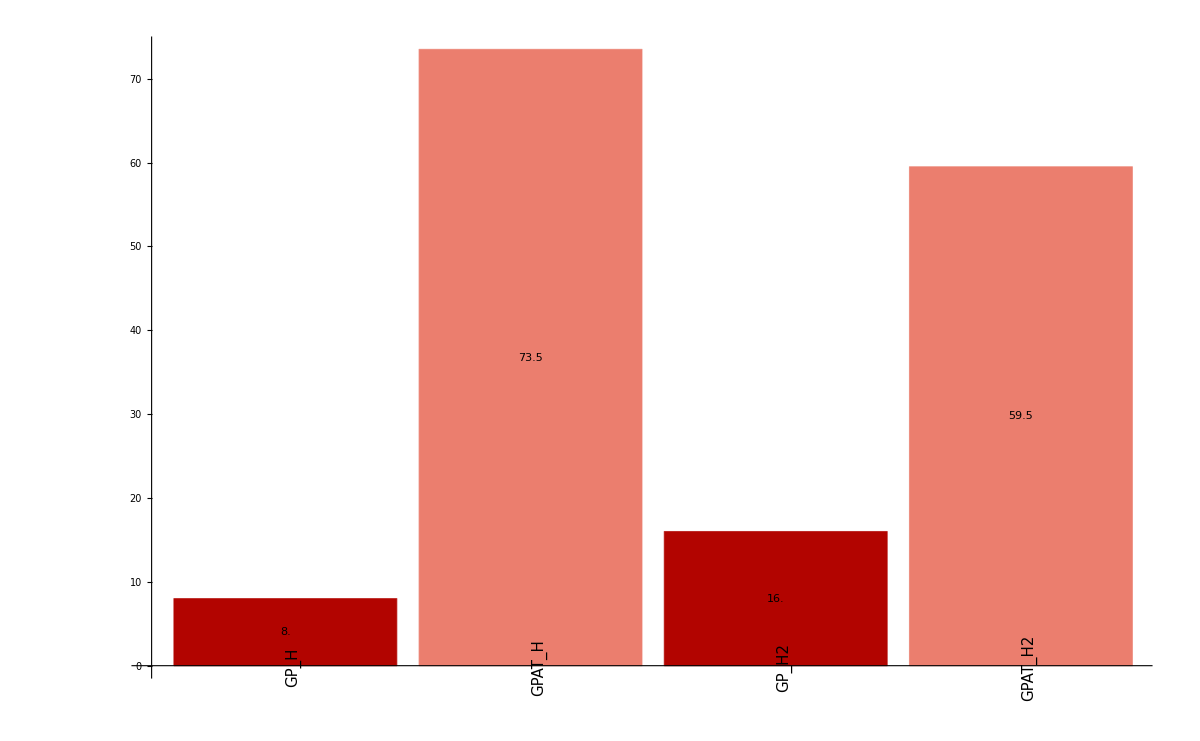

```mathematica
plotBooleanAsBarChart[sortedData,"SUCCESS",2]
```

```mathematica
plotAsBoxWhiskerChart[sortedData,"BSF"];
```

```mathematica
testMannWhitney[data,"GPAT_H","GPAT_H2","BSF"]
```

median 1: 0.952853

median 2: 0.949325

mean 1: 0.754262

mean 2: 0.528663

variance 1: 0.135817

variance 2: 0.222969

higher/lower variance ratio: 1.64169

U stat: 22636

P-value: 0.0226329

The null hypothesis that the median difference is 0 is rejected at the 5. percent level based on the Mann-Whitney test.

```mathematica
testKruskalWallis[data,{"GPAT_H","GPAT_H2"},"BSF"]
```

| GPAT_H | GPAT_H2
Mean | 0.754262 | 0.528663
Variance | 0.952853 | 0.949325
Variance | 0.135817 | 0.222969

LocationEquivalenceTest::ntsymmd: The p-value in 1.14305×10^-13, resulting from a test for symmetry, is below 0.05. The tests in {"KruskalWallis"} require that the data is symmetric about a common median.

| Statistic | P-Value
Kruskal-Wallis | 5.19838 | 0.0224202

```mathematica
testFisherExact[sortedData,"GPAT_H","GPAT_H2","SUCCESS",TwoSided->True]
```

| GPAT_H | GPAT_H2
true | 133. | 100.
false | 67. | 100.

0.00114716

```mathematica
sortConfigurationResults[sortedData,"GPAT_H2","BSF",10]
```

35 | 0.999122
104 | 0.992806
127 | 0.992407
77 | 0.990201
7 | 0.989773
130 | 0.989232
58 | 0.987287
152 | 0.986837
107 | 0.986168
111 | 0.986059

```mathematica
sortConfigurationResults[sortedData,"GPAT_H2","BSF",10,Output->"BSFGenomes"]//MatrixForm
```

Part::partw: Part 5 of {92977, 92850, {times[plus[0.996802\ times[times[plus[« 1 »], x2, x0, 1], plus[Times[« 2 »], 0.947061], 1], -1.00218\ x1]]}, 0.999122} does not exist.

Part::partw: Part 5 of {42070, 41956, {plus[1.00019\ times[times[times[plus[« 2 »], x0, x2, x1, 1], 1], 1], -0.989288\ x1]}, 0.992806} does not exist.

Part::partw: Part 5 of {50322, 50202, {plus[0.998577\ times[times[x0, x1, plus[Times[« 2 »], 1.00121]], x2, 1], 0.00761319, -0.997097\ x1]}, 0.992407} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Gen | Genome | Sorted | Simplified | f
92977 | Grid[{forestAsTreeForm[0.999122]}] | Grid[{forestAsTreeForm[sortForest[0.999122]]}] | Grid[{forestAsTreeFormSimplified[0.999122]}] | {92977,92850,{times[plus[0.996802 times[times[plus[1.05938 times[x1,1]],x2,x0,1],plus[0.946978 x1,0.947061],1],-1.00218 x1]]},0.999122}⟦5⟧
42070 | Grid[{forestAsTreeForm[0.992806]}] | Grid[{forestAsTreeForm[sortForest[0.992806]]}] | Grid[{forestAsTreeFormSimplified[0.992806]}] | {42070,41956,{plus[1.00019 times[times[times[plus[0.99968,0.999821 x1],x0,x2,x1,1],1],1],-0.989288 x1]},0.992806}⟦5⟧
50322 | Grid[{forestAsTreeForm[0.992407]}] | Grid[{forestAsTreeForm[sortForest[0.992407]]}] | Grid[{forestAsTreeFormSimplified[0.992407]}] | {50322,50202,{plus[0.998577 times[times[x0,x1,plus[1.00145 x1,1.00121]],x2,1],0.00761319,-0.997097 x1]},0.992407}⟦5⟧
48177 | Grid[{forestAsTreeForm[0.990201]}] | Grid[{forestAsTreeForm[sortForest[0.990201]]}] | Grid[{forestAsTreeFormSimplified[0.990201]}] | {48177,48083,{times[times[plus[1.00001 times[times[x2,x1,1,x1,x0],1],0.999802 times[1,times[1,x2],x1,x0],-1.00702 x1,0.0594502,-0.000492995 x0],1],1]},0.990201}⟦5⟧
35204 | Grid[{forestAsTreeForm[0.989773]}] | Grid[{forestAsTreeForm[sortForest[0.989773]]}] | Grid[{forestAsTreeFormSimplified[0.989773]}] | {35204,35101,{times[plus[0.999973 times[x2,x0,x1,x1,1],-0.996283 x1,1.00023 times[x2,x1,x0],-0.00140722]]},0.989773}⟦5⟧
96477 | Grid[{forestAsTreeForm[0.989232]}] | Grid[{forestAsTreeForm[sortForest[0.989232]]}] | Grid[{forestAsTreeFormSimplified[0.989232]}] | {96477,96373,{times[times[plus[0.999996 times[1,x2,x1,x0,x1],-0.00197473 x2,4.54093 times[plus[3.72673 x0,-3.5065 x0],x1,x2,1],-0.278508 sin[x2],-1.00493 x1],1]]},0.989232}⟦5⟧
46092 | Grid[{forestAsTreeForm[0.987287]}] | Grid[{forestAsTreeForm[sortForest[0.987287]]}] | Grid[{forestAsTreeFormSimplified[0.987287]}] | {46092,45986,{plus[1. times[plus[1.00627 times[times[1,x0,x1,x2,plus[0.99374 x1,0.994017]],1],0.0235175,-0.99806 x1]]]},0.987287}⟦5⟧
38853 | Grid[{forestAsTreeForm[0.986837]}] | Grid[{forestAsTreeForm[sortForest[0.986837]]}] | Grid[{forestAsTreeFormSimplified[0.986837]}] | {38853,38756,{times[plus[1.00001 times[x0,1,x2,x1,x1],1.00036 times[x1,x2,x0],-0.000354537 x0,-1.00362 x1,-0.0342898],1]},0.986837}⟦5⟧
60005 | Grid[{forestAsTreeForm[0.986168]}] | Grid[{forestAsTreeForm[sortForest[0.986168]]}] | Grid[{forestAsTreeFormSimplified[0.986168]}] | {60005,59902,{times[plus[0.999965 times[times[x2,1,x0,x1,x1],1],0.999912 times[x2,1,x0,x1],-1.0057 x1,-0.0604098]]},0.986168}⟦5⟧
86407 | Grid[{forestAsTreeForm[0.986059]}] | Grid[{forestAsTreeForm[sortForest[0.986059]]}] | Grid[{forestAsTreeFormSimplified[0.986059]}] | {86407,86302,{times[times[plus[1.00002 times[times[x0,1,x1,x1,x2],1],0.999986 times[x1,x0,x2],-0.0689196,-1.00547 x1,-0.00808085 x2,0.00879866 x0],1]]},0.986059}⟦5⟧

```mathematica
Export["GPAT_H2.pdf",%]
```

GPAT_H2.pdf